## Functions

```mathematica
g[k_]:=1/(1+k^2/a^2);
```

## Scattering Amplitude

```mathematica
G0[En_,H_]={{1/(En-H-ⅈ ϵ),0},{0,1/(En-H-β^2/m-ⅈ ϵ)}};
λ={{λo,λx},{λx,λc}};
```

```mathematica
Jmat[En_]=Limit[Integrate[G0[En,q^2/m]*g[q]g[q]*4π q^2/(2π)^3,{q,0,∞},Assumptions->{m>0,a>0,β≥0,En∈Reals,ϵ>0}],ϵ->0];
```

```mathematica
Δmat[En_]=IdentityMatrix[2]-λ.Jmat[En];

τ[En_]=Inverse[Δmat[En]].λ;
```

```mathematica
f[p_]=-m/(4π)Simplify[τ[p^2/m][[1,1]]g[p]g[p]]/. 1/(√(-p^2))->1/(-ⅈ p)/.√(-p^2)->-ⅈ p;
```

## Effective Range Expansion

```mathematica
ERE[p_,β_]=Series[1/f[p],{p,0,2}]+ⅈ p//Normal;
```

```mathematica
p0[β_]=Simplify[Coefficient[ERE[p,β],p,0]]/.√(β^2)->β/.√(1/β^2)->1/β
p1[β_]=Simplify[Coefficient[ERE[p,β],p,1]]/.√(β^2)->β/.√(1/β^2)->1/β
p2[β_]=Simplify[Coefficient[ERE[p,β],p,2]]/.√(β^2)->β/.√(1/β^2)->1/β
```

-(64 π^2 β^2+8 a^3 m π (λc+λo)+16 a^2 π (4 π+m β λo)+8 a π (16 π β+m β^2 λo)+a^4 m^2 (λc λo-λx^2))/(2 m (8 a^2 π λo+16 a π β λo+8 π β^2 λo+a^3 m (λc λo-λx^2)))

0

-(1024 π^3 β^6 λo+256 a^2 π^2 β^4 λo (24 π-m β λo)+64 a π^2 β^4 λo (64 π β-m β^2 λo)-a^7 m^3 β^2 (-λc λo+λx^2)^2+128 a^3 π^2 (32 π (β^2)^(3/2) λo+m β^4 (2 λc λo-3 λo^2-λx^2))+16 a^4 π (64 π^2 β^2 λo+16 m π (β^2)^(3/2) (2 λc λo-λo^2-λx^2)+m^2 β^4 λo (-λc λo+λx^2))+32 a^5 m π (2 π β^2 (4 λc λo-λo^2-λx^2)+m (β^2)^(3/2) λo (-λc λo+λx^2))+16 a^6 m π (4 π β λx^2+m β^2 (λc^2 λo+λo λx^2-λc (λo^2+λx^2))))/(2 a^2 m β^2 (8 a^2 π λo+16 a π β λo+8 π β^2 λo+a^3 m (λc λo-λx^2))^2)

```mathematica
T1[β_]=-1/p0[β]
```

(2 m (8 a^2 π λo+16 a π β λo+8 π β^2 λo+a^3 m (λc λo-λx^2)))/(64 π^2 β^2+8 a^3 m π (λc+λo)+16 a^2 π (4 π+m β λo)+8 a π (16 π β+m β^2 λo)+a^4 m^2 (λc λo-λx^2))

```mathematica
soln=Solve[p0[β]==0,β];
```

{{β→-3.92471},{β→0.524705}}

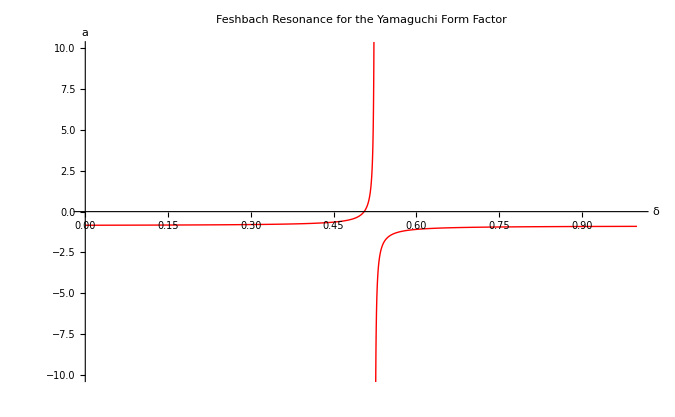

```mathematica
Params={λo->-.5,λc->-2,λx->-.1,m->4π,a->1.7};

soln/.Params

Bb=Plot[T1[β]/.Params,{β,0,1},PlotRange->All,AxesOrigin->{0,0},PlotStyle->Red,Exclusions->{β/.soln[[2]]/.Params}];

Graph=Show[Bb,PlotRange->{-10,10},AxesLabel->{"δ","a"},PlotLabel->"Feshbach Resonance for the Yamaguchi Form Factor"]
```

```mathematica
Export["/home/cnewby/SeniorDesign/LippmannSchwinger/SingleYama.eps",Graph]
```

/home/cnewby/SeniorDesign/LippmannSchwinger/SingleYama.eps